```mathematica
(*
  Twist Chain Simulation
Jihwan Myung 2016-2017
For
"The Choroid Plexus is an Important Circadian Clock Component"
By
Jihwan Myung, Christoph Schmal, Sungho Hong, Yoshiaki Tsukizawa, Pia Rose, Yong Zhang, Michael J.Holtzman, Erik De Schutter,Hanspeter Herzel,Grigory Bordyugov,Toru Takumi 
 Nature Communications (2018)
*)
```

```mathematica
(* Call the basic analysis package, FFTPeriod is the function that will be used *)
<<PMTAnalysis`
```

```mathematica
(* Graph display settings *)
SetOptions[ListPlot,BaseStyle->Directive[FontFamily->"Helvetica",FontSize->16],Frame->{True,True,False,False},FrameStyle->Directive[Black,AbsoluteThickness[1.1]],Axes->None,PlotMarkers->Automatic];
```

```mathematica
SetOptions[Plot,BaseStyle->Directive[FontFamily->"Helvetica",FontSize->16],Frame->{True,True,False,False},FrameStyle->Directive[Black,AbsoluteThickness[1.1]],Axes->None];
```

```mathematica
(* 4 random seeds make 4 replicate sets *)
```

```mathematica
normPer=25.5; (* Mean period *)
stdPer=1; (* Standard deviation of period *)
stdPha=1; (* Standard deviation of inital phases *)
```

```mathematica
(* Gaussian period distribution and initial phases *)
```

```mathematica
Table[omega[n]=2Pi/RandomReal[NormalDistribution[normPer,stdPer]],{n,1,11}]
```

{0.223615,0.247719,0.235188,0.240885,0.255269,0.254127,0.242477,0.246088,0.245526,0.246724,0.253987}

```mathematica
Table[initphi[n]=RandomReal[NormalDistribution[0,stdPha]],{n,1,11}]
```

{-0.868773,-2.53219,0.222036,-0.314145,-0.0320744,-1.40252,-0.81969,0.0685009,2.4925,1.05758,1.47064}

```mathematica
(* Poincare oscillator parameters *)
```

```mathematica
Table[A[n]=1,{n,1,11}]; (* Amplitude *)
Table[lambda[n]=0.02,{n,1,11}];
Table[epsilon[n]=-0.01,{n,1,11}];
```

```mathematica
r1[t_]:=Sqrt[x1[t]^2+y1[t]^2];
r2[t_]:=Sqrt[x2[t]^2+y2[t]^2];
r3[t_]:=Sqrt[x3[t]^2+y3[t]^2];
r4[t_]:=Sqrt[x4[t]^2+y4[t]^2];
r5[t_]:=Sqrt[x5[t]^2+y5[t]^2];
r6[t_]:=Sqrt[x6[t]^2+y6[t]^2];
r7[t_]:=Sqrt[x7[t]^2+y7[t]^2];
```

```mathematica
phi1[t_]:=ArcTan[x1[t],y1[t]];
phi2[t_]:=ArcTan[x2[t],y2[t]];
phi3[t_]:=ArcTan[x3[t],y3[t]];
phi4[t_]:=ArcTan[x4[t],y4[t]];
phi5[t_]:=ArcTan[x5[t],y5[t]];
phi6[t_]:=ArcTan[x6[t],y6[t]];
phi7[t_]:=ArcTan[x7[t],y7[t]];
```

```mathematica
coupling1[t_]:=0.0025*If[t<24*30,1,0];
coupling2[t_]:=0.0025*If[t<24*30,1,0];
coupling3[t_]:=0.0025*If[t<24*30,1,0];
coupling4[t_]:=0.0025*If[t<24*30,1,0];
coupling5[t_]:=0.0025*If[t<24*30,1,0];
coupling6[t_]:=0.0025*If[t<24*30,1,0];
coupling7[t_]:=0.0025*If[t<24*30,1,0];
```

```mathematica
(* ODE solver *)
```

```mathematica
Table[
nsol1[q]=NDSolve[{
x1'[t]==(A[1]-r1[t])*(lambda[1]*x1[t]-epsilon[1]*y1[t])-omega[1]*y1[t]+q*coupling2[t]*x2[t],
y1'[t]==(A[1]-r1[t])*(lambda[1]*y1[t]+epsilon[1]*x1[t])+omega[1]*x1[t]+q*coupling2[t]*y2[t],

x2'[t]==(A[2]-r2[t])*(lambda[2]*x2[t]-epsilon[2]*y2[t])-omega[2]*y2[t]+q*coupling1[t]*x1[t]+q*coupling3[t]*x3[t],
y2'[t]==(A[2]-r2[t])*(lambda[2]*y2[t]+epsilon[2]*x2[t])+omega[2]*x2[t]+q*coupling1[t]*y1[t]+q*coupling3[t]*y3[t],

x3'[t]==(A[3]-r3[t])*(lambda[3]*x3[t]-epsilon[3]*y3[t])-omega[3]*y3[t]+q*coupling2[t]*x2[t]+q*coupling4[t]*x4[t],
y3'[t]==(A[3]-r3[t])*(lambda[3]*y3[t]+epsilon[3]*x3[t])+omega[3]*x3[t]+q*coupling2[t]*y2[t]+q*coupling4[t]*y4[t],

x4'[t]==(A[4]-r4[t])*(lambda[4]*x4[t]-epsilon[4]*y4[t])-omega[4]*y4[t]+q*coupling3[t]*x3[t]+q*coupling5[t]*x5[t],
y4'[t]==(A[4]-r4[t])*(lambda[4]*y4[t]+epsilon[4]*x4[t])+omega[4]*x4[t]+q*coupling3[t]*y3[t]+q*coupling5[t]*y5[t],

x5'[t]==(A[5]-r5[t])*(lambda[5]*x5[t]-epsilon[5]*y5[t])-omega[5]*y5[t]+q*coupling4[t]*x4[t]+q*coupling6[t]*x6[t],
y5'[t]==(A[5]-r5[t])*(lambda[5]*y5[t]+epsilon[5]*x5[t])+omega[5]*x5[t]+q*coupling4[t]*y4[t]+q*coupling6[t]*y6[t],

x6'[t]==(A[6]-r6[t])*(lambda[6]*x6[t]-epsilon[6]*y6[t])-omega[6]*y6[t]+q*coupling5[t]*x5[t]+q*coupling7[t]*x7[t],
y6'[t]==(A[6]-r6[t])*(lambda[6]*y6[t]+epsilon[6]*x6[t])+omega[6]*x6[t]+q*coupling5[t]*y5[t]+q*coupling7[t]*y7[t],

x7'[t]==(A[7]-r7[t])*(lambda[7]*x7[t]-epsilon[7]*y7[t])-omega[7]*y7[t]+q*coupling6[t]*x6[t],
y7'[t]==(A[7]-r7[t])*(lambda[7]*y7[t]+epsilon[7]*x7[t])+omega[7]*x7[t]+q*coupling6[t]*y6[t],

x1[-24*30]==A[1]*Cos[(2Pi/24)*initphi[1]],y1[-24*30]==A[1]*Sin[(2Pi/24)*initphi[1]],
x2[-24*30]==A[2]*Cos[(2Pi/24)*initphi[2]],y2[-24*30]==A[2]*Sin[(2Pi/24)*initphi[2]],
x3[-24*30]==A[3]*Cos[(2Pi/24)*initphi[3]],y3[-24*30]==A[3]*Sin[(2Pi/24)*initphi[3]],
x4[-24*30]==A[4]*Cos[(2Pi/24)*initphi[4]],y4[-24*30]==A[4]*Sin[(2Pi/24)*initphi[4]],
x5[-24*30]==A[5]*Cos[(2Pi/24)*initphi[5]],y5[-24*30]==A[5]*Sin[(2Pi/24)*initphi[5]],
x6[-24*30]==A[6]*Cos[(2Pi/24)*initphi[6]],y6[-24*30]==A[6]*Sin[(2Pi/24)*initphi[6]],
x7[-24*30]==A[7]*Cos[(2Pi/24)*initphi[7]],y7[-24*30]==A[7]*Sin[(2Pi/24)*initphi[7]]
},

{x1[t],y1[t],
x2[t],y2[t],
x3[t],y3[t],
x4[t],y4[t],
x5[t],y5[t],
x6[t],y6[t],
x7[t],y7[t]},

{t,-24*30,24*60}];,
{q,0,10}];
```

```mathematica
(* Repeats for other replicates follow *)
```

```mathematica
Table[omega[n]=2Pi/RandomReal[NormalDistribution[normPer,stdPer]],{n,1,11}]
```

{0.256385,0.237908,0.245286,0.247212,0.250756,0.246792,0.231892,0.246214,0.241394,0.226777,0.244953}

```mathematica
Table[initphi[n]=RandomReal[NormalDistribution[0,stdPha]],{n,1,11}]
```

{-0.0903171,-0.170939,-0.715383,-0.00613965,0.9369,-0.719553,0.410309,0.522,-0.846057,0.902696,0.904404}

```mathematica
Table[
nsol2[q]=NDSolve[{
x1'[t]==(A[1]-r1[t])*(lambda[1]*x1[t]-epsilon[1]*y1[t])-omega[1]*y1[t]+q*coupling2[t]*x2[t],
y1'[t]==(A[1]-r1[t])*(lambda[1]*y1[t]+epsilon[1]*x1[t])+omega[1]*x1[t]+q*coupling2[t]*y2[t],

x2'[t]==(A[2]-r2[t])*(lambda[2]*x2[t]-epsilon[2]*y2[t])-omega[2]*y2[t]+q*coupling1[t]*x1[t]+q*coupling3[t]*x3[t],
y2'[t]==(A[2]-r2[t])*(lambda[2]*y2[t]+epsilon[2]*x2[t])+omega[2]*x2[t]+q*coupling1[t]*y1[t]+q*coupling3[t]*y3[t],

x3'[t]==(A[3]-r3[t])*(lambda[3]*x3[t]-epsilon[3]*y3[t])-omega[3]*y3[t]+q*coupling2[t]*x2[t]+q*coupling4[t]*x4[t],
y3'[t]==(A[3]-r3[t])*(lambda[3]*y3[t]+epsilon[3]*x3[t])+omega[3]*x3[t]+q*coupling2[t]*y2[t]+q*coupling4[t]*y4[t],

x4'[t]==(A[4]-r4[t])*(lambda[4]*x4[t]-epsilon[4]*y4[t])-omega[4]*y4[t]+q*coupling3[t]*x3[t]+q*coupling5[t]*x5[t],
y4'[t]==(A[4]-r4[t])*(lambda[4]*y4[t]+epsilon[4]*x4[t])+omega[4]*x4[t]+q*coupling3[t]*y3[t]+q*coupling5[t]*y5[t],

x5'[t]==(A[5]-r5[t])*(lambda[5]*x5[t]-epsilon[5]*y5[t])-omega[5]*y5[t]+q*coupling4[t]*x4[t]+q*coupling6[t]*x6[t],
y5'[t]==(A[5]-r5[t])*(lambda[5]*y5[t]+epsilon[5]*x5[t])+omega[5]*x5[t]+q*coupling4[t]*y4[t]+q*coupling6[t]*y6[t],

x6'[t]==(A[6]-r6[t])*(lambda[6]*x6[t]-epsilon[6]*y6[t])-omega[6]*y6[t]+q*coupling5[t]*x5[t]+q*coupling7[t]*x7[t],
y6'[t]==(A[6]-r6[t])*(lambda[6]*y6[t]+epsilon[6]*x6[t])+omega[6]*x6[t]+q*coupling5[t]*y5[t]+q*coupling7[t]*y7[t],

x7'[t]==(A[7]-r7[t])*(lambda[7]*x7[t]-epsilon[7]*y7[t])-omega[7]*y7[t]+q*coupling6[t]*x6[t],
y7'[t]==(A[7]-r7[t])*(lambda[7]*y7[t]+epsilon[7]*x7[t])+omega[7]*x7[t]+q*coupling6[t]*y6[t],

x1[-24*30]==A[1]*Cos[(2Pi/24)*initphi[1]],y1[-24*30]==A[1]*Sin[(2Pi/24)*initphi[1]],
x2[-24*30]==A[2]*Cos[(2Pi/24)*initphi[2]],y2[-24*30]==A[2]*Sin[(2Pi/24)*initphi[2]],
x3[-24*30]==A[3]*Cos[(2Pi/24)*initphi[3]],y3[-24*30]==A[3]*Sin[(2Pi/24)*initphi[3]],
x4[-24*30]==A[4]*Cos[(2Pi/24)*initphi[4]],y4[-24*30]==A[4]*Sin[(2Pi/24)*initphi[4]],
x5[-24*30]==A[5]*Cos[(2Pi/24)*initphi[5]],y5[-24*30]==A[5]*Sin[(2Pi/24)*initphi[5]],
x6[-24*30]==A[6]*Cos[(2Pi/24)*initphi[6]],y6[-24*30]==A[6]*Sin[(2Pi/24)*initphi[6]],
x7[-24*30]==A[7]*Cos[(2Pi/24)*initphi[7]],y7[-24*30]==A[7]*Sin[(2Pi/24)*initphi[7]]
},

{x1[t],y1[t],
x2[t],y2[t],
x3[t],y3[t],
x4[t],y4[t],
x5[t],y5[t],
x6[t],y6[t],
x7[t],y7[t]},

{t,-24*30,24*60}];,
{q,0,10}];
```

```mathematica
Table[omega[n]=2Pi/RandomReal[NormalDistribution[normPer,stdPer]],{n,1,11}]
```

{0.244556,0.250836,0.246124,0.241123,0.253703,0.253865,0.261927,0.247901,0.242347,0.241722,0.245712}

```mathematica
Table[initphi[n]=RandomReal[NormalDistribution[0,stdPha]],{n,1,11}]
```

{0.974696,-0.809635,0.765135,1.03951,0.341017,0.181307,-1.06573,-0.615934,1.75476,-0.614022,0.42123}

```mathematica
Table[
nsol3[q]=NDSolve[{
x1'[t]==(A[1]-r1[t])*(lambda[1]*x1[t]-epsilon[1]*y1[t])-omega[1]*y1[t]+q*coupling2[t]*x2[t],
y1'[t]==(A[1]-r1[t])*(lambda[1]*y1[t]+epsilon[1]*x1[t])+omega[1]*x1[t]+q*coupling2[t]*y2[t],

x2'[t]==(A[2]-r2[t])*(lambda[2]*x2[t]-epsilon[2]*y2[t])-omega[2]*y2[t]+q*coupling1[t]*x1[t]+q*coupling3[t]*x3[t],
y2'[t]==(A[2]-r2[t])*(lambda[2]*y2[t]+epsilon[2]*x2[t])+omega[2]*x2[t]+q*coupling1[t]*y1[t]+q*coupling3[t]*y3[t],

x3'[t]==(A[3]-r3[t])*(lambda[3]*x3[t]-epsilon[3]*y3[t])-omega[3]*y3[t]+q*coupling2[t]*x2[t]+q*coupling4[t]*x4[t],
y3'[t]==(A[3]-r3[t])*(lambda[3]*y3[t]+epsilon[3]*x3[t])+omega[3]*x3[t]+q*coupling2[t]*y2[t]+q*coupling4[t]*y4[t],

x4'[t]==(A[4]-r4[t])*(lambda[4]*x4[t]-epsilon[4]*y4[t])-omega[4]*y4[t]+q*coupling3[t]*x3[t]+q*coupling5[t]*x5[t],
y4'[t]==(A[4]-r4[t])*(lambda[4]*y4[t]+epsilon[4]*x4[t])+omega[4]*x4[t]+q*coupling3[t]*y3[t]+q*coupling5[t]*y5[t],

x5'[t]==(A[5]-r5[t])*(lambda[5]*x5[t]-epsilon[5]*y5[t])-omega[5]*y5[t]+q*coupling4[t]*x4[t]+q*coupling6[t]*x6[t],
y5'[t]==(A[5]-r5[t])*(lambda[5]*y5[t]+epsilon[5]*x5[t])+omega[5]*x5[t]+q*coupling4[t]*y4[t]+q*coupling6[t]*y6[t],

x6'[t]==(A[6]-r6[t])*(lambda[6]*x6[t]-epsilon[6]*y6[t])-omega[6]*y6[t]+q*coupling5[t]*x5[t]+q*coupling7[t]*x7[t],
y6'[t]==(A[6]-r6[t])*(lambda[6]*y6[t]+epsilon[6]*x6[t])+omega[6]*x6[t]+q*coupling5[t]*y5[t]+q*coupling7[t]*y7[t],

x7'[t]==(A[7]-r7[t])*(lambda[7]*x7[t]-epsilon[7]*y7[t])-omega[7]*y7[t]+q*coupling6[t]*x6[t],
y7'[t]==(A[7]-r7[t])*(lambda[7]*y7[t]+epsilon[7]*x7[t])+omega[7]*x7[t]+q*coupling6[t]*y6[t],

x1[-24*30]==A[1]*Cos[(2Pi/24)*initphi[1]],y1[-24*30]==A[1]*Sin[(2Pi/24)*initphi[1]],
x2[-24*30]==A[2]*Cos[(2Pi/24)*initphi[2]],y2[-24*30]==A[2]*Sin[(2Pi/24)*initphi[2]],
x3[-24*30]==A[3]*Cos[(2Pi/24)*initphi[3]],y3[-24*30]==A[3]*Sin[(2Pi/24)*initphi[3]],
x4[-24*30]==A[4]*Cos[(2Pi/24)*initphi[4]],y4[-24*30]==A[4]*Sin[(2Pi/24)*initphi[4]],
x5[-24*30]==A[5]*Cos[(2Pi/24)*initphi[5]],y5[-24*30]==A[5]*Sin[(2Pi/24)*initphi[5]],
x6[-24*30]==A[6]*Cos[(2Pi/24)*initphi[6]],y6[-24*30]==A[6]*Sin[(2Pi/24)*initphi[6]],
x7[-24*30]==A[7]*Cos[(2Pi/24)*initphi[7]],y7[-24*30]==A[7]*Sin[(2Pi/24)*initphi[7]]
},

{x1[t],y1[t],
x2[t],y2[t],
x3[t],y3[t],
x4[t],y4[t],
x5[t],y5[t],
x6[t],y6[t],
x7[t],y7[t]},

{t,-24*30,24*60}];,
{q,0,10}];
```

```mathematica
Table[omega[n]=2Pi/RandomReal[NormalDistribution[normPer,stdPer]],{n,1,11}]
```

{0.243363,0.259637,0.250116,0.240009,0.260286,0.246961,0.259242,0.254165,0.246418,0.241125,0.249765}

```mathematica
Table[initphi[n]=RandomReal[NormalDistribution[0,stdPha]],{n,1,11}]
```

{-1.6997,0.288404,-1.35889,0.595916,0.3993,-0.0466144,0.3629,1.10141,-0.0195339,-0.26982,1.43848}

```mathematica
Table[
nsol4[q]=NDSolve[{
x1'[t]==(A[1]-r1[t])*(lambda[1]*x1[t]-epsilon[1]*y1[t])-omega[1]*y1[t]+q*coupling2[t]*x2[t],
y1'[t]==(A[1]-r1[t])*(lambda[1]*y1[t]+epsilon[1]*x1[t])+omega[1]*x1[t]+q*coupling2[t]*y2[t],

x2'[t]==(A[2]-r2[t])*(lambda[2]*x2[t]-epsilon[2]*y2[t])-omega[2]*y2[t]+q*coupling1[t]*x1[t]+q*coupling3[t]*x3[t],
y2'[t]==(A[2]-r2[t])*(lambda[2]*y2[t]+epsilon[2]*x2[t])+omega[2]*x2[t]+q*coupling1[t]*y1[t]+q*coupling3[t]*y3[t],

x3'[t]==(A[3]-r3[t])*(lambda[3]*x3[t]-epsilon[3]*y3[t])-omega[3]*y3[t]+q*coupling2[t]*x2[t]+q*coupling4[t]*x4[t],
y3'[t]==(A[3]-r3[t])*(lambda[3]*y3[t]+epsilon[3]*x3[t])+omega[3]*x3[t]+q*coupling2[t]*y2[t]+q*coupling4[t]*y4[t],

x4'[t]==(A[4]-r4[t])*(lambda[4]*x4[t]-epsilon[4]*y4[t])-omega[4]*y4[t]+q*coupling3[t]*x3[t]+q*coupling5[t]*x5[t],
y4'[t]==(A[4]-r4[t])*(lambda[4]*y4[t]+epsilon[4]*x4[t])+omega[4]*x4[t]+q*coupling3[t]*y3[t]+q*coupling5[t]*y5[t],

x5'[t]==(A[5]-r5[t])*(lambda[5]*x5[t]-epsilon[5]*y5[t])-omega[5]*y5[t]+q*coupling4[t]*x4[t]+q*coupling6[t]*x6[t],
y5'[t]==(A[5]-r5[t])*(lambda[5]*y5[t]+epsilon[5]*x5[t])+omega[5]*x5[t]+q*coupling4[t]*y4[t]+q*coupling6[t]*y6[t],

x6'[t]==(A[6]-r6[t])*(lambda[6]*x6[t]-epsilon[6]*y6[t])-omega[6]*y6[t]+q*coupling5[t]*x5[t]+q*coupling7[t]*x7[t],
y6'[t]==(A[6]-r6[t])*(lambda[6]*y6[t]+epsilon[6]*x6[t])+omega[6]*x6[t]+q*coupling5[t]*y5[t]+q*coupling7[t]*y7[t],

x7'[t]==(A[7]-r7[t])*(lambda[7]*x7[t]-epsilon[7]*y7[t])-omega[7]*y7[t]+q*coupling6[t]*x6[t],
y7'[t]==(A[7]-r7[t])*(lambda[7]*y7[t]+epsilon[7]*x7[t])+omega[7]*x7[t]+q*coupling6[t]*y6[t],

x1[-24*30]==A[1]*Cos[(2Pi/24)*initphi[1]],y1[-24*30]==A[1]*Sin[(2Pi/24)*initphi[1]],
x2[-24*30]==A[2]*Cos[(2Pi/24)*initphi[2]],y2[-24*30]==A[2]*Sin[(2Pi/24)*initphi[2]],
x3[-24*30]==A[3]*Cos[(2Pi/24)*initphi[3]],y3[-24*30]==A[3]*Sin[(2Pi/24)*initphi[3]],
x4[-24*30]==A[4]*Cos[(2Pi/24)*initphi[4]],y4[-24*30]==A[4]*Sin[(2Pi/24)*initphi[4]],
x5[-24*30]==A[5]*Cos[(2Pi/24)*initphi[5]],y5[-24*30]==A[5]*Sin[(2Pi/24)*initphi[5]],
x6[-24*30]==A[6]*Cos[(2Pi/24)*initphi[6]],y6[-24*30]==A[6]*Sin[(2Pi/24)*initphi[6]],
x7[-24*30]==A[7]*Cos[(2Pi/24)*initphi[7]],y7[-24*30]==A[7]*Sin[(2Pi/24)*initphi[7]]
},

{x1[t],y1[t],
x2[t],y2[t],
x3[t],y3[t],
x4[t],y4[t],
x5[t],y5[t],
x6[t],y6[t],
x7[t],y7[t]},

{t,-24*30,24*60}];,
{q,0,10}];
```

```mathematica
Table[omega[n]=2Pi/RandomReal[NormalDistribution[normPer,stdPer]],{n,1,11}]
```

{0.258831,0.230266,0.242269,0.242421,0.249346,0.247775,0.244212,0.24045,0.23011,0.2394,0.253344}

```mathematica
Table[initphi[n]=RandomReal[NormalDistribution[0,stdPha]],{n,1,11}]
```

{-1.03284,-0.338963,1.51759,0.456746,0.555399,0.0112673,-0.842118,0.504675,-0.32915,1.86048,-1.15381}

```mathematica
Table[
nsol5[q]=NDSolve[{
x1'[t]==(A[1]-r1[t])*(lambda[1]*x1[t]-epsilon[1]*y1[t])-omega[1]*y1[t]+q*coupling2[t]*x2[t],
y1'[t]==(A[1]-r1[t])*(lambda[1]*y1[t]+epsilon[1]*x1[t])+omega[1]*x1[t]+q*coupling2[t]*y2[t],

x2'[t]==(A[2]-r2[t])*(lambda[2]*x2[t]-epsilon[2]*y2[t])-omega[2]*y2[t]+q*coupling1[t]*x1[t]+q*coupling3[t]*x3[t],
y2'[t]==(A[2]-r2[t])*(lambda[2]*y2[t]+epsilon[2]*x2[t])+omega[2]*x2[t]+q*coupling1[t]*y1[t]+q*coupling3[t]*y3[t],

x3'[t]==(A[3]-r3[t])*(lambda[3]*x3[t]-epsilon[3]*y3[t])-omega[3]*y3[t]+q*coupling2[t]*x2[t]+q*coupling4[t]*x4[t],
y3'[t]==(A[3]-r3[t])*(lambda[3]*y3[t]+epsilon[3]*x3[t])+omega[3]*x3[t]+q*coupling2[t]*y2[t]+q*coupling4[t]*y4[t],

x4'[t]==(A[4]-r4[t])*(lambda[4]*x4[t]-epsilon[4]*y4[t])-omega[4]*y4[t]+q*coupling3[t]*x3[t]+q*coupling5[t]*x5[t],
y4'[t]==(A[4]-r4[t])*(lambda[4]*y4[t]+epsilon[4]*x4[t])+omega[4]*x4[t]+q*coupling3[t]*y3[t]+q*coupling5[t]*y5[t],

x5'[t]==(A[5]-r5[t])*(lambda[5]*x5[t]-epsilon[5]*y5[t])-omega[5]*y5[t]+q*coupling4[t]*x4[t]+q*coupling6[t]*x6[t],
y5'[t]==(A[5]-r5[t])*(lambda[5]*y5[t]+epsilon[5]*x5[t])+omega[5]*x5[t]+q*coupling4[t]*y4[t]+q*coupling6[t]*y6[t],

x6'[t]==(A[6]-r6[t])*(lambda[6]*x6[t]-epsilon[6]*y6[t])-omega[6]*y6[t]+q*coupling5[t]*x5[t]+q*coupling7[t]*x7[t],
y6'[t]==(A[6]-r6[t])*(lambda[6]*y6[t]+epsilon[6]*x6[t])+omega[6]*x6[t]+q*coupling5[t]*y5[t]+q*coupling7[t]*y7[t],

x7'[t]==(A[7]-r7[t])*(lambda[7]*x7[t]-epsilon[7]*y7[t])-omega[7]*y7[t]+q*coupling6[t]*x6[t],
y7'[t]==(A[7]-r7[t])*(lambda[7]*y7[t]+epsilon[7]*x7[t])+omega[7]*x7[t]+q*coupling6[t]*y6[t],

x1[-24*30]==A[1]*Cos[(2Pi/24)*initphi[1]],y1[-24*30]==A[1]*Sin[(2Pi/24)*initphi[1]],
x2[-24*30]==A[2]*Cos[(2Pi/24)*initphi[2]],y2[-24*30]==A[2]*Sin[(2Pi/24)*initphi[2]],
x3[-24*30]==A[3]*Cos[(2Pi/24)*initphi[3]],y3[-24*30]==A[3]*Sin[(2Pi/24)*initphi[3]],
x4[-24*30]==A[4]*Cos[(2Pi/24)*initphi[4]],y4[-24*30]==A[4]*Sin[(2Pi/24)*initphi[4]],
x5[-24*30]==A[5]*Cos[(2Pi/24)*initphi[5]],y5[-24*30]==A[5]*Sin[(2Pi/24)*initphi[5]],
x6[-24*30]==A[6]*Cos[(2Pi/24)*initphi[6]],y6[-24*30]==A[6]*Sin[(2Pi/24)*initphi[6]],
x7[-24*30]==A[7]*Cos[(2Pi/24)*initphi[7]],y7[-24*30]==A[7]*Sin[(2Pi/24)*initphi[7]]
},

{x1[t],y1[t],
x2[t],y2[t],
x3[t],y3[t],
x4[t],y4[t],
x5[t],y5[t],
x6[t],y6[t],
x7[t],y7[t]},

{t,-24*30,24*60}];,
{q,0,10}];
```

```mathematica
(* Data *)
```

```mathematica
s1[1]=Table[Table[Sin[phi1[t]]/.nsol1[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s1[2]=Table[Table[Sin[phi2[t]]/.nsol1[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s1[3]=Table[Table[Sin[phi3[t]]/.nsol1[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s1[4]=Table[Table[Sin[phi4[t]]/.nsol1[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s1[5]=Table[Table[Sin[phi5[t]]/.nsol1[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s1[6]=Table[Table[Sin[phi6[t]]/.nsol1[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s1[7]=Table[Table[Sin[phi7[t]]/.nsol1[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
```

```mathematica
s2[1]=Table[Table[Sin[phi1[t]]/.nsol2[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s2[2]=Table[Table[Sin[phi2[t]]/.nsol2[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s2[3]=Table[Table[Sin[phi3[t]]/.nsol2[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s2[4]=Table[Table[Sin[phi4[t]]/.nsol2[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s2[5]=Table[Table[Sin[phi5[t]]/.nsol2[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s2[6]=Table[Table[Sin[phi6[t]]/.nsol2[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s2[7]=Table[Table[Sin[phi7[t]]/.nsol2[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
```

```mathematica
s3[1]=Table[Table[Sin[phi1[t]]/.nsol3[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s3[2]=Table[Table[Sin[phi2[t]]/.nsol3[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s3[3]=Table[Table[Sin[phi3[t]]/.nsol3[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s3[4]=Table[Table[Sin[phi4[t]]/.nsol3[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s3[5]=Table[Table[Sin[phi5[t]]/.nsol3[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s3[6]=Table[Table[Sin[phi6[t]]/.nsol3[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s3[7]=Table[Table[Sin[phi7[t]]/.nsol3[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
```

```mathematica
s4[1]=Table[Table[Sin[phi1[t]]/.nsol4[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s4[2]=Table[Table[Sin[phi2[t]]/.nsol4[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s4[3]=Table[Table[Sin[phi3[t]]/.nsol4[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s4[4]=Table[Table[Sin[phi4[t]]/.nsol4[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s4[5]=Table[Table[Sin[phi5[t]]/.nsol4[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s4[6]=Table[Table[Sin[phi6[t]]/.nsol4[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s4[7]=Table[Table[Sin[phi7[t]]/.nsol4[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
```

```mathematica
s5[1]=Table[Table[Sin[phi1[t]]/.nsol5[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s5[2]=Table[Table[Sin[phi2[t]]/.nsol5[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s5[3]=Table[Table[Sin[phi3[t]]/.nsol5[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s5[4]=Table[Table[Sin[phi4[t]]/.nsol5[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s5[5]=Table[Table[Sin[phi5[t]]/.nsol5[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s5[6]=Table[Table[Sin[phi6[t]]/.nsol5[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
s5[7]=Table[Table[Sin[phi7[t]]/.nsol5[n],{t,24*0,24*60,0.25}]//Flatten,{n,0,10}];
```

```mathematica
(* Results *)
```

```mathematica
amptableA=
{Table[r1[t]/.nsol1[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r2[t]/.nsol1[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r3[t]/.nsol1[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r4[t]/.nsol1[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r5[t]/.nsol1[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r6[t]/.nsol1[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r7[t]/.nsol1[n],{t,{24*30}},{n,0,10}]//Flatten}
```

{{1.,1.06812,1.02779,1.0151,1.21167,0.968333,1.34279,1.65925,1.85787,1.83848,2.05011},{1.,1.00503,1.16964,1.39847,1.65867,1.74288,2.02081,2.32173,2.53518,2.53389,2.80968},{1.,0.903021,1.35103,1.61468,1.92244,2.12804,2.3591,2.62664,2.76711,2.6245,3.03051},{1.,0.869562,1.32703,1.46734,1.9408,2.16393,2.38493,2.65723,2.69033,2.05271,2.94627},{1.,1.04239,1.30651,1.45647,1.87616,2.12509,2.36803,2.62692,2.63837,2.29043,3.09936},{1.,1.08989,1.25214,1.29301,1.64269,1.92697,2.19519,2.43308,2.57699,2.77669,3.16254},{1.,0.947524,1.05358,0.628258,1.24631,1.47899,1.69004,1.87253,2.07715,2.32508,2.51477}}

```mathematica
amptableB=
{Table[r1[t]/.nsol2[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r2[t]/.nsol2[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r3[t]/.nsol2[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r4[t]/.nsol2[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r5[t]/.nsol2[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r6[t]/.nsol2[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r7[t]/.nsol2[n],{t,{24*30}},{n,0,10}]//Flatten}
```

{{1.,0.992105,1.07716,1.28038,1.50124,1.6919,1.87184,2.04595,2.22163,2.39662,2.56952},{1.,1.00797,1.1418,1.53977,1.83256,2.09036,2.3351,2.57207,2.80679,3.03982,3.27082},{1.,1.00648,1.13945,1.6348,1.92994,2.19544,2.4487,2.69338,2.93847,3.18479,3.42997},{1.,1.03073,1.2644,1.6673,1.94599,2.20011,2.43457,2.6576,2.90523,3.16336,3.41854},{1.,1.12853,1.37756,1.61968,1.82961,2.05774,2.2431,2.42049,2.68636,2.97189,3.24469},{1.,1.06018,1.23061,1.25597,1.40587,1.64634,1.73138,1.91836,2.26825,2.59407,2.88189},{1.,0.933997,0.893143,0.560714,0.883686,1.11256,0.977866,1.29817,1.67686,1.95185,2.17968}}

```mathematica
amptableC=
{Table[r1[t]/.nsol3[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r2[t]/.nsol3[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r3[t]/.nsol3[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r4[t]/.nsol3[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r5[t]/.nsol3[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r6[t]/.nsol3[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r7[t]/.nsol3[n],{t,{24*30}},{n,0,10}]//Flatten}
```

{{0.999999,1.01798,1.2394,1.38008,1.54831,1.69499,1.84948,2.008,2.16935,2.33245,2.49663},{0.999999,1.12795,1.38913,1.64757,1.88847,2.09632,2.3117,2.53025,2.75154,2.97463,3.19882},{0.999999,1.18586,1.30911,1.68185,1.96754,2.15854,2.38915,2.62678,2.86832,3.11196,3.35661},{0.999999,1.03322,1.05167,1.41755,1.92292,1.92589,2.18525,2.46451,2.74195,3.01488,3.28353},{0.999999,1.03101,0.995573,1.13929,1.90784,1.65575,2.01544,2.35032,2.65891,2.95041,3.2306},{0.999999,1.10586,1.10231,1.33108,1.89694,1.73489,2.08322,2.38356,2.65911,2.92057,3.17318},{0.999999,1.01492,0.981944,1.24469,1.56953,1.53758,1.76976,1.97515,2.16764,2.3528,2.53335}}

```mathematica
amptableD=
{Table[r1[t]/.nsol4[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r2[t]/.nsol4[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r3[t]/.nsol4[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r4[t]/.nsol4[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r5[t]/.nsol4[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r6[t]/.nsol4[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r7[t]/.nsol4[n],{t,{24*30}},{n,0,10}]//Flatten}
```

{{0.999999,0.973941,1.09017,0.923886,1.25333,1.51257,1.71776,1.90644,2.08741,2.26409,2.43812},{0.999999,0.993874,1.19064,1.37068,1.69312,1.98062,2.23554,2.47909,2.7169,2.95132,3.18355},{0.999999,1.11963,1.09876,1.5692,1.8893,2.16348,2.42037,2.67192,2.92079,3.16807,3.41429},{0.999999,1.18575,0.984461,1.13262,1.70376,2.05871,2.35335,2.6288,2.89487,3.15551,3.41268},{0.999999,1.11479,1.17518,1.17213,1.69634,2.04807,2.33984,2.61199,2.87452,3.13148,3.38489},{0.999999,1.07697,1.26338,1.5527,1.82709,2.09416,2.34004,2.57784,2.81146,3.04263,3.27223},{0.999999,1.07345,1.16416,1.35328,1.52356,1.71774,1.89781,2.07209,2.2434,2.41302,2.58161}}

```mathematica
amptableE=
{Table[r1[t]/.nsol5[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r2[t]/.nsol5[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r3[t]/.nsol5[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r4[t]/.nsol5[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r5[t]/.nsol5[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r6[t]/.nsol5[n],{t,{24*30}},{n,0,10}]//Flatten,
Table[r7[t]/.nsol5[n],{t,{24*30}},{n,0,10}]//Flatten}
```

{{0.999999,1.0478,1.09419,1.24315,1.22368,1.54377,1.76983,1.97136,2.16136,2.34483,2.52416},{0.999999,1.0938,0.940552,1.20226,1.61329,1.90456,2.18815,2.45097,2.7023,2.94667,3.18652},{0.999999,1.17672,1.11931,1.29559,1.7521,1.96567,2.26187,2.54014,2.80726,3.0676,3.32358},{0.999999,1.20097,1.40393,1.58293,1.21577,1.87683,2.23793,2.54264,2.82486,3.09558,3.35958},{0.999999,1.1599,1.43558,1.67232,1.21976,1.97246,2.30991,2.59717,2.86623,3.12638,3.38147},{0.999999,1.03032,1.37643,1.63953,1.76809,2.0816,2.33322,2.57045,2.80247,3.03199,3.26013},{0.999999,0.942395,1.19202,1.37602,1.5604,1.74092,1.90584,2.06946,2.23318,2.39724,2.56162}}

```mathematica
pertableA1=Median[Table[
{Table[FFTPeriod[s1[1][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[1][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s1[2][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[2][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s1[3][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[3][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s1[4][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[4][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s1[5][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[5][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s1[6][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[6][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s1[7][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[7][[1]][[1;;24*30]]]}]],{n,1,11}]},{q,1,60}]]
```

{{28.1739,28.2599,27.847,27.5042,26.3951,25.,25.2238,24.9135,24.7612,24.6951,24.1791},{25.3323,25.1602,25.9096,25.5219,25.3918,25.0483,24.9327,24.7517,24.6388,24.7801,24.1521},{26.7216,26.3415,25.7962,25.4917,25.2336,25.0096,24.8466,24.5967,24.4621,24.7612,24.2152},{26.1396,26.4598,26.203,25.2533,25.0386,24.8181,24.6294,24.3792,24.1611,24.5083,24.3976},{24.6014,24.5176,24.5269,24.7045,24.6951,24.5548,24.2788,24.1611,23.806,23.0934,24.0713},{24.7328,24.6201,24.8276,24.3061,24.5083,24.3884,24.0803,23.9556,23.6152,23.1843,24.0178},{25.8373,25.92,25.1944,27.113,24.4436,24.1972,24.0267,23.7624,23.5294,23.3766,24.0089}}

```mathematica
pertableB1=Median[Table[
{Table[FFTPeriod[s2[1][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[1][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s2[2][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[2][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s2[3][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[3][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s2[4][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[4][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s2[5][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[5][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s2[6][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[6][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s2[7][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[7][[1]][[1;;24*30]]]}]],{n,1,11}]},{q,1,60}]]
```

{{24.4713,24.6014,24.3609,24.9423,24.714,24.4621,24.3701,24.0982,23.9822,23.7276,23.538},{26.3951,25.9096,26.6228,24.9231,24.714,24.4713,24.3792,24.0892,24.0089,23.7102,23.5465},{25.6532,25.3125,25.0193,24.9231,24.714,24.4713,24.3792,24.0982,24.0089,23.7189,23.5422},{25.4018,25.3422,25.0871,24.8944,24.6951,24.4805,24.3701,24.1071,24.0178,23.7276,23.5465},{25.0483,25.1944,25.0774,24.8562,24.6388,24.4621,24.3701,24.1071,24.0356,23.7102,23.5636},{25.4018,25.2927,25.1748,25.,24.5548,24.3609,24.3152,24.1972,24.0089,23.7189,23.5894},{27.0677,26.799,26.3951,26.1924,27.7279,24.4436,24.2606,24.2334,23.9291,23.806,23.5551}}

```mathematica
pertableC1=Median[Table[
{Table[FFTPeriod[s3[1][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[1][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s3[2][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[2][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s3[3][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[3][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s3[4][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[4][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s3[5][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[5][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s3[6][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[6][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s3[7][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[7][[1]][[1;;24*30]]]}]],{n,1,11}]},{q,1,60}]]
```

{{25.7449,25.4118,25.126,24.8562,24.5734,24.3609,24.0089,23.8762,23.6152,23.3851,23.1843},{25.029,25.4317,25.2042,24.8848,24.5548,24.3701,24.0356,23.8323,23.6496,23.3851,23.1843},{25.4617,25.4917,25.2533,24.9423,24.5827,24.3792,24.0535,23.806,23.6583,23.3851,23.1926},{26.0555,25.7041,24.9711,25.0386,24.6201,24.3792,24.0803,23.7885,23.6583,23.3851,23.1926},{24.7706,24.7801,24.4436,26.0346,24.7612,24.2697,24.1251,23.7973,23.6066,23.402,23.1926},{24.7612,24.8848,24.3517,23.7711,24.5083,24.297,24.0267,23.8586,23.5722,23.4104,23.1926},{24.0445,23.9114,24.3701,24.1341,24.3976,24.3152,23.9734,23.8762,23.5636,23.4104,23.1926}}

```mathematica
pertableD1=Median[Table[
{Table[FFTPeriod[s4[1][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[1][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s4[2][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[2][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s4[3][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[3][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s4[4][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[4][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s4[5][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[5][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s4[6][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[6][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s4[7][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[7][[1]][[1;;24*30]]]}]],{n,1,11}]},{q,1,60}]]
```

{{25.7552,25.6939,25.1455,27.2957,24.3152,24.,23.8762,23.6066,23.3851,23.1926,23.0277},{24.1431,24.2515,24.7612,24.2788,24.3517,24.0445,23.7885,23.6496,23.3766,23.1926,23.0114},{25.0968,24.9231,24.714,24.5548,24.3609,24.0356,23.7885,23.6496,23.3766,23.1926,23.0032},{26.2348,25.6329,25.2927,24.714,24.3517,24.0178,23.7973,23.641,23.3766,23.1926,23.0114},{24.0982,24.5548,24.6388,24.4713,24.2334,24.0982,23.758,23.641,23.3851,23.1926,22.9869},{25.4018,24.8848,24.5176,24.4805,24.2243,24.0892,23.7537,23.641,23.3851,23.1926,22.995},{24.1972,24.4252,24.4991,24.4991,24.1881,24.0892,23.7624,23.6324,23.3851,23.1926,22.9869}}

```mathematica
pertableE1=Median[Table[
{Table[FFTPeriod[s5[1][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[1][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s5[2][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[2][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s5[3][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[3][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s5[4][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[4][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s5[5][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[5][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s5[6][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[6][[1]][[1;;24*30]]]}]],{n,1,11}],
Table[FFTPeriod[s5[7][[n]][[1;;24*30]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[7][[1]][[1;;24*30]]]}]],{n,1,11}]},{q,1,60}]]
```

{{24.3152,24.3701,24.2062,23.8674,25.0871,24.7991,24.4898,24.3426,24.0178,23.8498,23.6496},{27.3302,27.598,27.3649,26.3094,25.1163,24.7896,24.5362,24.3243,23.9911,23.885,23.6238},{25.8683,25.7654,25.5118,25.6431,25.0968,24.7896,24.4991,24.3426,24.0089,23.8498,23.6496},{25.8373,26.1396,25.6634,25.2336,25.1163,24.7801,24.4805,24.3061,24.0624,23.806,23.6756},{25.1748,25.2435,25.2336,25.1065,25.0096,24.7423,24.4991,24.2424,24.0982,23.7798,23.6756},{25.4018,25.4217,25.2042,25.1065,24.9519,24.714,24.5083,24.2243,24.1071,23.7798,23.6756},{25.7859,25.362,25.214,25.0677,24.9327,24.7045,24.4805,24.2424,24.0892,23.7798,23.6756}}

```mathematica
pertableA2=Median[Table[
{Table[FFTPeriod[s1[1][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[1][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s1[2][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[2][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s1[3][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[3][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s1[4][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[4][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s1[5][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[5][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s1[6][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[6][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s1[7][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[7][[1]][[24*31;;24*60]]]}]],{n,1,11}]},{q,1,60}]]
```

{{28.0685,28.1335,27.5965,27.2988,27.9136,25.3342,24.7055,24.7357,24.6054,24.4174,24.3782},{25.4191,25.5797,25.8739,25.5689,25.1767,25.0417,24.8369,24.7156,24.4371,24.3002,24.5457},{26.7634,26.1863,25.8629,25.5366,25.1662,25.0314,24.847,24.7458,24.388,24.1648,24.7963},{26.0515,26.1751,25.6553,26.2429,25.135,25.052,24.7458,24.6453,24.3002,23.974,25.4617},{24.5755,24.6254,24.5061,24.2516,24.8878,24.5755,24.5358,24.2807,24.069,23.7769,23.0329},{24.7559,24.4371,24.3978,24.6955,24.766,24.4568,24.4076,24.1744,23.9362,23.6288,23.6841},{25.9292,25.9624,25.7751,24.8878,24.516,24.4076,24.3099,24.1072,23.8422,23.5099,23.8703}}

```mathematica
pertableB2=Median[Table[
{Table[FFTPeriod[s2[1][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[1][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s2[2][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[2][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s2[3][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[3][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s2[4][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[4][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s2[5][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[5][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s2[6][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[6][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s2[7][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[7][[1]][[24*31;;24*60]]]}]],{n,1,11}]},{q,1,60}]]
```

{{24.5656,24.5755,24.8572,24.898,24.6453,24.5656,24.3002,24.1552,23.9456,23.7769,23.5555},{26.3683,26.1863,26.2316,24.8572,24.7256,24.5358,24.2905,24.1648,23.9551,23.7862,23.5373},{25.5904,25.5045,24.9389,24.8572,24.6804,24.5457,24.2905,24.1648,23.9551,23.7862,23.5555},{25.451,25.2499,25.0934,24.9286,24.6654,24.5457,24.2905,24.1744,23.9551,23.7862,23.5555},{25.0211,25.3131,25.1246,24.9902,24.7055,24.5656,24.2905,24.184,23.9645,23.7862,23.5373},{25.5045,25.1454,25.052,24.847,24.898,24.6453,24.3196,24.184,23.9835,23.7676,23.4917},{27.128,27.3356,27.3111,26.7516,25.4724,24.898,24.3684,24.1648,23.9835,23.7211,23.5281}}

```mathematica
pertableC2=Median[Table[
{Table[FFTPeriod[s3[1][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[1][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s3[2][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[2][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s3[3][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[3][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s3[4][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[4][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s3[5][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[5][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s3[6][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[6][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s3[7][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[7][[1]][[24*31;;24*60]]]}]],{n,1,11}]},{q,1,60}]]
```

{{25.677,25.4084,25.2499,24.9082,24.5457,24.2905,24.0786,23.8142,23.6197,23.4554,23.1912},{25.0727,25.3554,25.2185,24.9594,24.6154,24.2905,24.069,23.8142,23.583,23.4464,23.2356},{25.5474,25.271,25.1454,24.9082,24.6254,24.3002,24.069,23.8235,23.5647,23.4283,23.2489},{26.0627,26.5644,24.9491,24.7256,24.6453,24.3099,24.069,23.8422,23.5647,23.3922,23.2578},{24.7862,24.516,24.6754,24.4174,24.9799,24.388,24.069,23.861,23.6105,23.3382,23.2178},{24.7559,24.6353,24.3978,24.0309,24.6054,24.3099,24.069,23.8422,23.6472,23.3472,23.1735},{23.9929,23.8329,24.3684,23.9173,24.5656,24.2807,24.0595,23.8142,23.6565,23.3652,23.1558}}

```mathematica
pertableD2=Median[Table[
{Table[FFTPeriod[s4[1][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[1][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s4[2][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[2][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s4[3][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[3][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s4[4][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[4][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s4[5][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[5][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s4[6][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[6][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s4[7][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[7][[1]][[24*31;;24*60]]]}]],{n,1,11}]},{q,1,60}]]
```

{{25.8189,25.6445,25.6337,24.9286,24.3099,24.05,23.7955,23.6105,23.4554,23.1823,22.9545},{24.2226,24.5855,24.6854,24.6854,24.2905,24.05,23.8142,23.5555,23.4283,23.24,22.9545},{25.1871,25.1038,24.847,24.5557,24.2807,24.05,23.8142,23.5555,23.4283,23.2489,22.9632},{26.1413,26.277,26.3226,24.9184,24.271,24.05,23.8048,23.5601,23.4283,23.24,22.9632},{24.136,24.2807,24.184,24.2323,24.3099,24.0404,23.8329,23.5647,23.3742,23.2578,22.9893},{25.4831,25.229,24.516,24.4076,24.3002,24.0404,23.8329,23.5555,23.3832,23.2578,22.9806},{24.2613,24.4076,24.5358,24.3978,24.2905,24.0404,23.8422,23.5647,23.3742,23.2578,22.9893}}

```mathematica
pertableE2=Median[Table[
{Table[FFTPeriod[s5[1][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[1][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s5[2][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[2][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s5[3][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[3][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s5[4][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[4][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s5[5][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[5][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s5[6][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[6][[1]][[24*31;;24*60]]]}]],{n,1,11}],
Table[FFTPeriod[s5[7][[n]][[24*31;;24*60]]+Table[RandomReal[NormalDistribution[0,0.01]],{t,1,Length[s1[7][[1]][[24*31;;24*60]]]}]],{n,1,11}]},{q,1,60}]]
```

{{24.271,24.3782,24.0977,24.8878,25.1662,24.8674,24.5557,24.2613,24.0595,23.8142,23.6197},{27.2988,26.7752,27.4468,25.5259,25.1767,24.8166,24.4962,24.2613,24.0595,23.8142,23.6472},{25.9402,25.8519,25.5689,25.7751,25.229,24.8674,24.5457,24.2613,24.0595,23.8142,23.6105},{25.9292,25.9402,25.9958,25.7642,25.1558,24.8064,24.5755,24.2807,24.05,23.8329,23.5921},{25.2395,25.0005,25.0417,25.0727,25.0417,24.6854,24.5259,24.3002,24.05,23.8516,23.583},{25.3448,25.229,25.2395,25.0624,25.052,24.6754,24.5061,24.3002,24.05,23.8516,23.583},{25.7423,25.4617,25.208,25.0934,25.0211,24.6654,24.516,24.2905,24.05,23.8422,23.583}}

```mathematica
(* Outputs *)
```

```mathematica
(* Coupling and amplitude *)
```

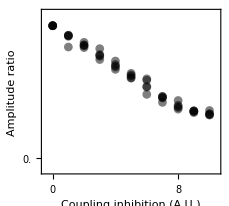

```mathematica
Show[ListPlot[dampA=Table[Total[amptableA[[All,n]]]/Total[amptableA[[All,11]]],{n,11,1,-1}],Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.1,1.1}},
FrameTicks->{Table[{n,(n-1),{0,0.02}},{n,1,20,2}],Table[{n,n,{0,0.02}},{n,0,10,0.2}]},FrameLabel->{"Coupling inhibition (A.U.)","Amplitude ratio"},PlotStyle->Opacity[0.5,Black]],
ListPlot[dampB=Table[Total[amptableB[[All,n]]]/Total[amptableB[[All,11]]],{n,11,1,-1}],Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.1,1.1}},
FrameTicks->{Table[{n,(n-1),{0,0.02}},{n,1,20}],Table[{n,n,{0,0.02}},{n,0,10,0.2}]},FrameLabel->{"Coupling inhibition (A.U.)","Amplitude ratio"},PlotStyle->Opacity[0.5,Black]],
ListPlot[dampC=Table[Total[amptableC[[All,n]]]/Total[amptableC[[All,11]]],{n,11,1,-1}],Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.1,1.1}},
FrameTicks->{Table[{n,(n-1),{0,0.02}},{n,1,20}],Table[{n,n,{0,0.02}},{n,0,10,0.2}]},FrameLabel->{"Coupling inhibition (A.U.)","Amplitude ratio"},PlotStyle->Opacity[0.5,Black]],
ListPlot[dampD=Table[Total[amptableD[[All,n]]]/Total[amptableD[[All,11]]],{n,11,1,-1}],Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.1,1.1}},
FrameTicks->{Table[{n,(n-1),{0,0.02}},{n,1,20}],Table[{n,n,{0,0.02}},{n,0,10,0.2}]},FrameLabel->{"Coupling inhibition (A.U.)","Amplitude ratio"},PlotStyle->Opacity[0.5,Black]],
ListPlot[dampE=Table[Total[amptableE[[All,n]]]/Total[amptableE[[All,11]]],{n,11,1,-1}],Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.1,1.1}},
FrameTicks->{Table[{n,(n-1),{0,0.02}},{n,1,20}],Table[{n,n,{0,0.02}},{n,0,10,0.2}]},FrameLabel->{"Coupling inhibition (A.U.)","Amplitude ratio"},PlotStyle->Opacity[0.5,Black]],ImageSize->230,AspectRatio->0.9]
```

```mathematica
(* Coupling and period *)
```

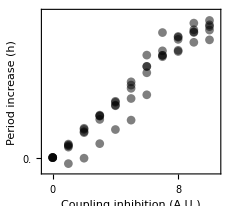

```mathematica
Show[ListPlot[dperA1=Table[Mean[pertableA1[[All,n]]]-Mean[pertableA1[[All,11]]],{n,11,1,-1}],Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.2,2.2}},
FrameTicks->{Table[{n,(n-1),{0,0.02}},{n,1,20,2}],Table[{n,n,{0,0.02}},{n,0,10,0.4}]},FrameLabel->{"Coupling inhibition (A.U.)","Period increase (h)"},PlotStyle->Opacity[0.5,Black]],
ListPlot[dperB1=Table[Mean[pertableB1[[All,n]]]-Mean[pertableB1[[All,11]]],{n,11,1,-1}],Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.1,2.1}},
FrameTicks->{Table[{n,(n-1),{0,0.02}},{n,1,20}],Table[{n,n,{0,0.02}},{n,0,10,0.4}]},FrameLabel->{"Coupling inhibition (A.U.)","Period increase (h)"},PlotStyle->Opacity[0.5,Black]],
ListPlot[dperC1=Table[Mean[pertableC1[[All,n]]]-Mean[pertableC1[[All,11]]],{n,11,1,-1}],Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.1,2.68}},
FrameTicks->{Table[{n,(n-1),{0,0.02}},{n,1,20}],Table[{n,n,{0,0.02}},{n,0,10,0.4}]},FrameLabel->{"Coupling inhibition (A.U.)","Period increase (h)"},PlotStyle->Opacity[0.5,Black]],
ListPlot[dperD1=Table[Mean[pertableD1[[All,n]]]-Mean[pertableD1[[All,11]]],{n,11,1,-1}],Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.1,2.68}},
FrameTicks->{Table[{n,(n-1),{0,0.02}},{n,1,20}],Table[{n,n,{0,0.02}},{n,0,10,0.4}]},FrameLabel->{"Coupling inhibition (A.U.)","Period increase (h)"},PlotStyle->Opacity[0.5,Black]],
ListPlot[dperE1=Table[Mean[pertableE1[[All,n]]]-Mean[pertableE1[[All,11]]],{n,11,1,-1}],Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.1,2.68}},
FrameTicks->{Table[{n,(n-1),{0,0.02}},{n,1,20}],Table[{n,n,{0,0.02}},{n,0,10,0.4}]},FrameLabel->{"Coupling inhibition (A.U.)","Period increase (h)"},PlotStyle->Opacity[0.5,Black]],ImageSize->230,AspectRatio->0.9]
```

```mathematica
(* Amplitude-Period relation *)
```

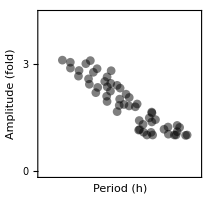

```mathematica
Show[
ListPlot[Thread[{cperA1,campA}],Joined->False,PlotMarkers->Automatic,PlotRange->{{22.5,26.2},{-0.1,4.4}},
FrameTicks->{Table[{n,n,{0,0.02}},{n,1,30}],Table[{n,n,{0,0.02}},{n,0,10}]},FrameLabel->{"Period (h)","Amplitude (fold)"},AspectRatio->1,ImageSize->210,PlotStyle->Opacity[0.5,Black]],
ListPlot[Thread[{cperB1,campB}],Joined->False,PlotMarkers->Automatic,PlotRange->{{22.5,26.2},{-0.1,4.4}},
FrameTicks->{Table[{n,n,{0,0.02}},{n,1,30}],Table[{n,n,{0,0.02}},{n,0,10}]},FrameLabel->{"Period (h)","Amplitude (fold)"},AspectRatio->1,ImageSize->210,PlotStyle->Opacity[0.5,Black]],
ListPlot[Thread[{cperC1,campC}],Joined->False,PlotMarkers->Automatic,PlotRange->{{22.5,26.2},{-0.1,4.4}},
FrameTicks->{Table[{n,n,{0,0.02}},{n,1,30}],Table[{n,n,{0,0.02}},{n,0,10}]},FrameLabel->{"Period (h)","Amplitude (fold)"},AspectRatio->1,ImageSize->210,PlotStyle->Opacity[0.5,Black]],
ListPlot[Thread[{cperD1,campD}],Joined->False,PlotMarkers->Automatic,PlotRange->{{22.5,26.2},{-0.1,4.4}},
FrameTicks->{Table[{n,n,{0,0.02}},{n,1,30}],Table[{n,n,{0,0.02}},{n,0,10}]},FrameLabel->{"Period (h)","Amplitude (fold)"},AspectRatio->1,ImageSize->210,PlotStyle->Opacity[0.5,Black]],
ListPlot[Thread[{cperE1,campE}],Joined->False,PlotMarkers->Automatic,PlotRange->{{22.5,26.2},{-0.1,4.4}},
FrameTicks->{Table[{n,n,{0,0.02}},{n,1,30}],Table[{n,n,{0,0.02}},{n,0,10}]},FrameLabel->{"Period (h)","Amplitude (fold)"},AspectRatio->1,ImageSize->210,PlotStyle->Opacity[0.5,Black]]]
```

```mathematica
(* Kuramoto Synchronization Index *)
```

```mathematica
Table[siA[q]=Table[Abs[(1/7)*(Exp[I*phi1[t]]+Exp[I*phi2[t]]+Exp[I*phi3[t]]+Exp[I*phi4[t]]+Exp[I*phi5[t]]+Exp[I*phi6[t]]+Exp[I*phi7[t]])/(Exp[I*(phi1[t]+phi2[t]+phi3[t]+phi4[t]+phi5[t]+phi6[t]+phi7[t])/7])]/.nsol1[q],{t,0,24*60,0.25}]//Flatten,{q,0,10}];
```

```mathematica
Table[siB[q]=Table[Abs[(1/7)*(Exp[I*phi1[t]]+Exp[I*phi2[t]]+Exp[I*phi3[t]]+Exp[I*phi4[t]]+Exp[I*phi5[t]]+Exp[I*phi6[t]]+Exp[I*phi7[t]])/(Exp[I*(phi1[t]+phi2[t]+phi3[t]+phi4[t]+phi5[t]+phi6[t]+phi7[t])/7])]/.nsol2[q],{t,0,24*60,0.25}]//Flatten,{q,0,10}];
```

```mathematica
Table[siC[q]=Table[Abs[(1/7)*(Exp[I*phi1[t]]+Exp[I*phi2[t]]+Exp[I*phi3[t]]+Exp[I*phi4[t]]+Exp[I*phi5[t]]+Exp[I*phi6[t]]+Exp[I*phi7[t]])/(Exp[I*(phi1[t]+phi2[t]+phi3[t]+phi4[t]+phi5[t]+phi6[t]+phi7[t])/7])]/.nsol3[q],{t,0,24*60,0.25}]//Flatten,{q,0,10}];
```

```mathematica
Table[siD[q]=Table[Abs[(1/7)*(Exp[I*phi1[t]]+Exp[I*phi2[t]]+Exp[I*phi3[t]]+Exp[I*phi4[t]]+Exp[I*phi5[t]]+Exp[I*phi6[t]]+Exp[I*phi7[t]])/(Exp[I*(phi1[t]+phi2[t]+phi3[t]+phi4[t]+phi5[t]+phi6[t]+phi7[t])/7])]/.nsol4[q],{t,0,24*60,0.25}]//Flatten,{q,0,10}];
```

```mathematica
Table[siE[q]=Table[Abs[(1/7)*(Exp[I*phi1[t]]+Exp[I*phi2[t]]+Exp[I*phi3[t]]+Exp[I*phi4[t]]+Exp[I*phi5[t]]+Exp[I*phi6[t]]+Exp[I*phi7[t]])/(Exp[I*(phi1[t]+phi2[t]+phi3[t]+phi4[t]+phi5[t]+phi6[t]+phi7[t])/7])]/.nsol5[q],{t,0,24*60,0.25}]//Flatten,{q,0,10}];
```

```mathematica
meanSiA=Table[Mean[siA[q][[4*24*25;;4*24*29]]],{q,0,10}];
meanSiB=Table[Mean[siB[q][[4*24*25;;4*24*29]]],{q,0,10}];
meanSiC=Table[Mean[siC[q][[4*24*25;;4*24*29]]],{q,0,10}];
meanSiD=Table[Mean[siD[q][[4*24*25;;4*24*29]]],{q,0,10}];
meanSiE=Table[Mean[siE[q][[4*24*25;;4*24*29]]],{q,0,10}];
```

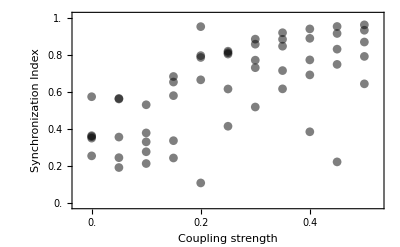

```mathematica
Show[ListPlot[meanSiA,Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.01,1.01}},
FrameTicks->{Table[{n,If[OddQ[n],(n-1)*0.05,""],{0,0.02}},{n,1,20}],Table[{n,n,{0,0.02}},{n,0,1,0.2}]},FrameLabel->{"Coupling strength","Synchronization Index"},PlotStyle->Opacity[0.5,Black]],
ListPlot[meanSiB,Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.01,1.01}},
FrameTicks->{Table[{n,If[OddQ[n],(n-1)*0.05,""],{0,0.02}},{n,1,20}],Table[{n,n,{0,0.02}},{n,0,1,0.2}]},FrameLabel->{"Coupling strength","Synchronization Index"},PlotStyle->Opacity[0.5,Black]],
ListPlot[meanSiC,Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.01,1.01}},
FrameTicks->{Table[{n,If[OddQ[n],(n-1)*0.05,""],{0,0.02}},{n,1,20}],Table[{n,n,{0,0.02}},{n,0,1,0.2}]},FrameLabel->{"Coupling strength","Synchronization Index"},PlotStyle->Opacity[0.5,Black]],
ListPlot[meanSiD,Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.01,1.01}},
FrameTicks->{Table[{n,If[OddQ[n],(n-1)*0.05,""],{0,0.02}},{n,1,20}],Table[{n,n,{0,0.02}},{n,0,1,0.2}]},FrameLabel->{"Coupling strength","Synchronization Index"},PlotStyle->Opacity[0.5,Black]],
ListPlot[meanSiE,Joined->False,PlotMarkers->Automatic,PlotRange->{{0.5,11.5},{-0.01,1.01}},
FrameTicks->{Table[{n,If[OddQ[n],(n-1)*0.05,""],{0,0.02}},{n,1,20}],Table[{n,n,{0,0.02}},{n,0,1,0.2}]},FrameLabel->{"Coupling strength","Synchronization Index"},PlotStyle->Opacity[0.5,Black]]]
```